### Categorization

Tutorial

Toolbox

Toolbox`

Toolbox/tutorial/Model construction and manipulation

### Keywords

Details

# Model construction and manipulation

The MASS Toolbox relies on a model structures

This loads the package.

```mathematica
Needs["Toolbox`"]
```

### Model construction

constructModel[{rxn_1,rxn_2, ...}] | construct a model from a list of reactions
constructModel[S,{m_1,m_2,...},{id_1,id_2,...}] | construct a model from stoichiometry matrix S, metabolites m and reaction identifiers

Constructing models.

Using a list of reactions to construct a model.

```mathematica
model=constructModel[{Overscript[x1⇌x2, 1],Overscript[x2⇌x3, 2],Overscript[x3⇌x4, 3]}]
```

Using a stoichiometry matrix construct a model.

```mathematica
model=constructModel[({{-1, 0, 0}, {1, -1, 0}, {0, 1, -1}, {0, 0, 1}}),{x1,x2,x3,x4},{"1","2","3"}];
```

### Model attributes

Models provide a series of attributes. Some of them are mutable, e.g, InitialConditions or Parameters, others are immutable, e.g., Species or Stoichiometry. Immutable attributes usually depend on other mutable attributes and thus can be modified indirectly.

model["Attributes"] | returns a list of all available attributes in model
getAttribute[model] | returns the respective attribute
model["Attribute"] | returns the respective attribute
setAttribute[model, new] | replaces the respective attribute enirely with new
updateAttribute[model, new] | adds non-existing information

Handling model attributes.

Get a list of all available attributes.

```mathematica
model["Attributes"]
```

{ID,Name,Constraints,InitialConditions,Parameters,GPR,BoundaryConditions,HasOnlySubstanceUnits,Constant,ReversibleColumnIndices,CustomRateLaws,CustomODE,ElementalComposition,Notes,Ignore,UnitChecking,Synonyms,Events,Objective,Stoichiometry,Species,Fluxes,Attributes,SparseStoichiometry,Reactions,Exchanges,Variables,ForwardRateConstants,ReverseRateConstants,EquilibriumConstants,IrreversibleColumnIndices,Rates,Compartments,ODE,Genes,Proteins,GeneAssociations,ProteinAssociations,Enzymes}

Initially, the model does not contain any initial conditions or parameters.

```mathematica
model["InitialConditions"]
model["Parameters"]
```

{}

{}

Using getter functions to access the same attributes.

```mathematica
getInitialConditions[model]
getParameters[model]
```

{}

{}

Using setter functions to include parameters and initial conditions. The model is changed in place.

```mathematica
setInitialConditions[model,{x1->1,x2->0,x3->0,x4->0}]
setParameters[model,{Subscript[k, 1]^⟶->1,Subscript[k, 2]^⟶->0.01,Subscript[k, 3]^⟶->0.0001,Underscript[K, 1]->1,Underscript[K, 2]->1}]
```

Initial conditions and parameters have been properly set.

```mathematica
model["InitialConditions"]
model["Parameters"]
```

{x1→1,x2→0,x3→0,x4→0}

{k_1^⟶→1,k_2^⟶→0.01,k_3^⟶→0.0001,K_1→1,K_2→1}

Attributes can also be provided during the model construction process.

constructModel[args,Attr_1 →{...}, ...] | provide additional information during model construction

Provide attribute information during model construction.

Set initial conditions and parameters during model construction

```mathematica
model=constructModel[{Overscript[x1⇌x2, 1],Overscript[x2⇌x3, 2],Overscript[x3->x4, 3]},InitialConditions->{x1->1,x2->0,x3->0,x4->0},Parameters->{Subscript[k, 1]^⟶->1,Subscript[k, 2]^⟶->0.01,Subscript[k, 3]^⟶->0.0001,Underscript[K, 1]->1,Underscript[K, 2]->1}];
```

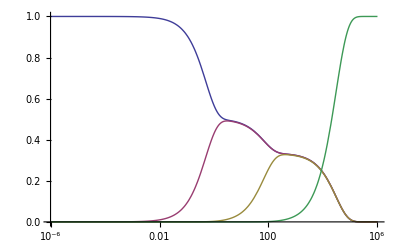

```mathematica
plotSimulation[simulate[model,{t,0,1*^6}][[1]],PlotFunction->LogLinearPlot]
```

Using updater functions to modify attributes

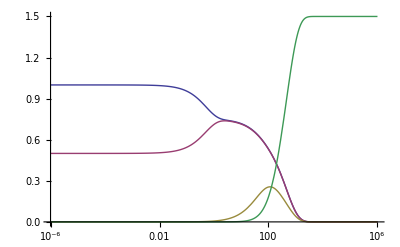

```mathematica
updateInitialConditions[model,{x2->0.5}]
updateParameters[model,{Subscript[k, 3]^⟶->0.01}]
plotSimulation[simulate[model,{t,0,1*^6}][[1]],PlotFunction->LogLinearPlot]
```

### Add and delete reactions

deleteReactions[model, {r_1,r_(2,)...}] | return new model with reactions deleted
addReactions[model, {r_2,r_2, ...}] | return new model reactions added

Change reaction content.

Add a reaction.

```mathematica
model2=addReactions[model,{Overscript[x4->x1, 4]}];
model2["Reactions"]
```

{(x1⇌x2)^1,(x2⇌x3)^2,(x3→x4)^3,(x4→x1)^4}

Delete the added reaction

```mathematica
model2=deleteReactions[model2,{"4"}];
model2["Reactions"]
```

{(x1⇌x2)^1,(x2⇌x3)^2,(x3→x4)^3}

```mathematica
Head[v["1"]]
```

v

```mathematica
FullForm[v["1"]*v["2"]]
```

Times[v["1"],v["2"]]

```mathematica
Times["a","b","c"]
```

a b c

```mathematica
MatchQ[v["1"]*v["2"],Times[__v]]
```

False

### Set operations

Union[model, model2, ...] | Unify models
Intersection[model, model2, ...] | Get the intersection of models
Complement[model, model2, ...] | Get the complement of models

Set operations for models.

Get the union of two model

```mathematica
model2=Union[model,model2];
model2["Reactions"]
```

Panic!

Panic!

{(x1⇌x2)^1,(x2⇌x3)^2,(x3→x4)^3}

More About

Related Tutorials

Related Wolfram Education Group Courses